```mathematica
g[y_]:=-100+20(k^2-k l+l^2)y+4(k^2-k l+l^2)^2y^2+k^2(k-l)^2l^2y^3
```

```mathematica
f[x_]:=g[x/(k^2-k l+l^2)]
```

```mathematica
f[x]
```

-100+20 x+4 x^2+(k^2 (k-l)^2 l^2 x^3)/((k^2-k l+l^2)^3)

```mathematica
Solve[-100+20x+4x^2+0x^3==0,x]
```

{{x→5/2 (-1-√5)},{x→5/2 (-1+√5)}}

```mathematica
f2[x_]:=-100+20 x+4 x^2+u x^3
u[t_]:=(1-t)^2t^2/(1-t+t^2)
Simplify[u[t]-u[1-t]]
u[1/2]
```

0

1/12

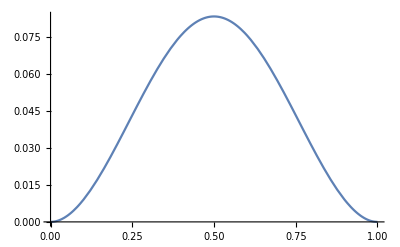

```mathematica
Plot[u[t],{t,0,1}]
```